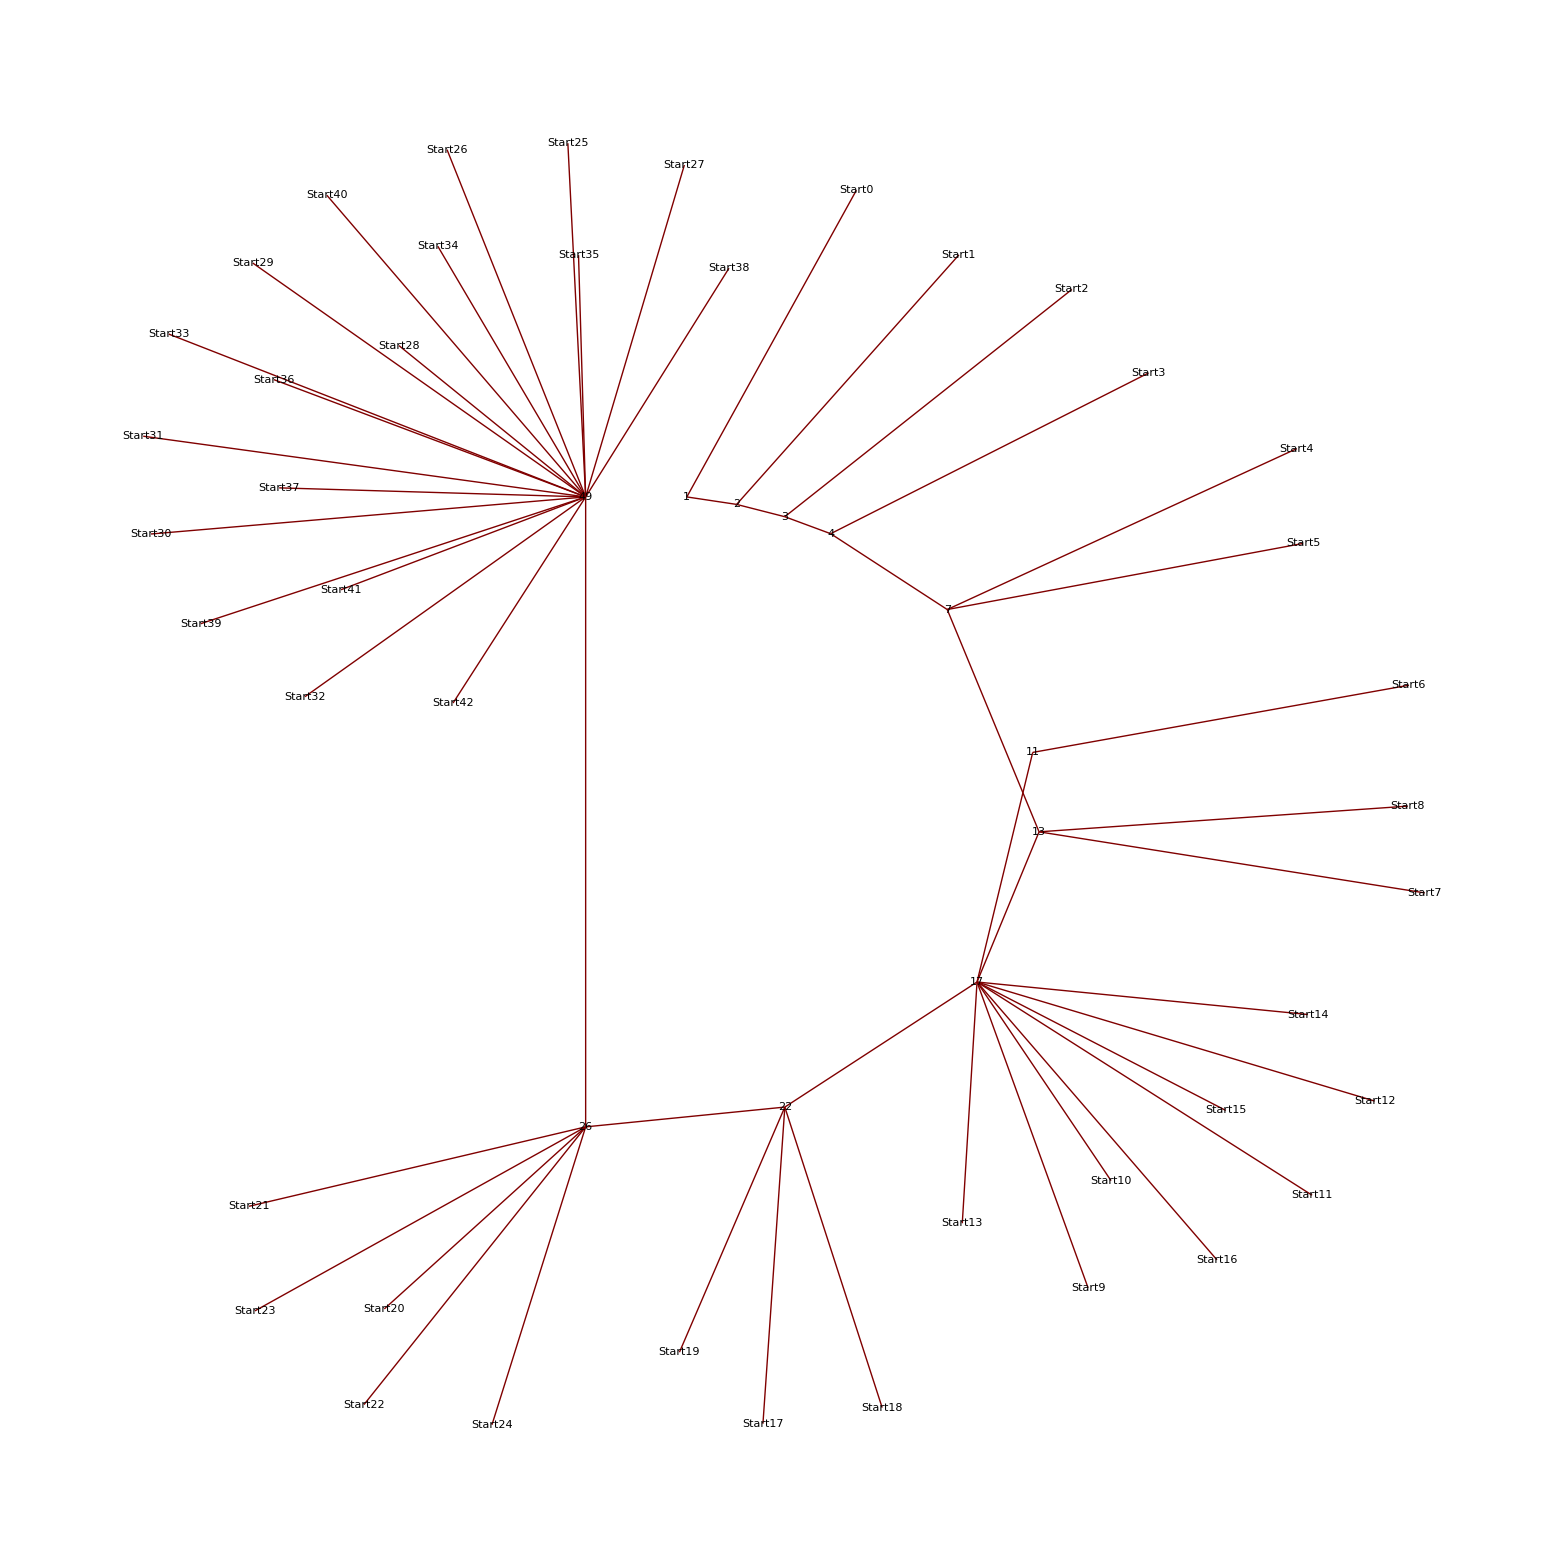

```mathematica
With[{range=50},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotes[VoteList[start,range,{7,11,13,17}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

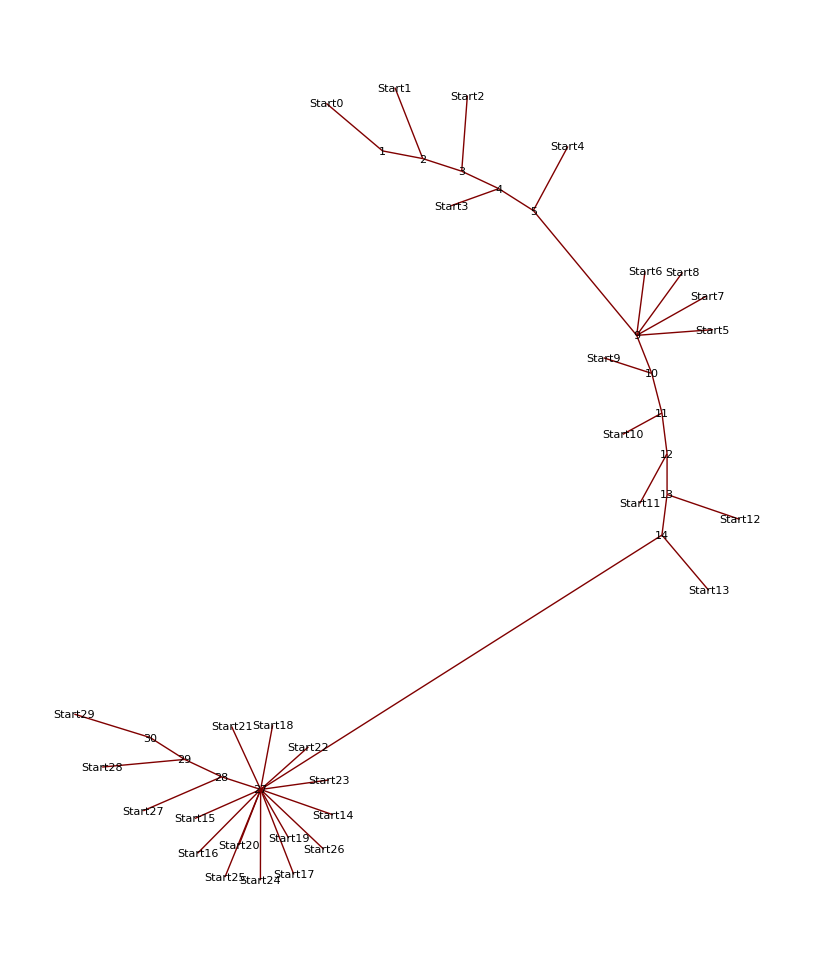

```mathematica
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotes[VoteList[start,range,{3}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

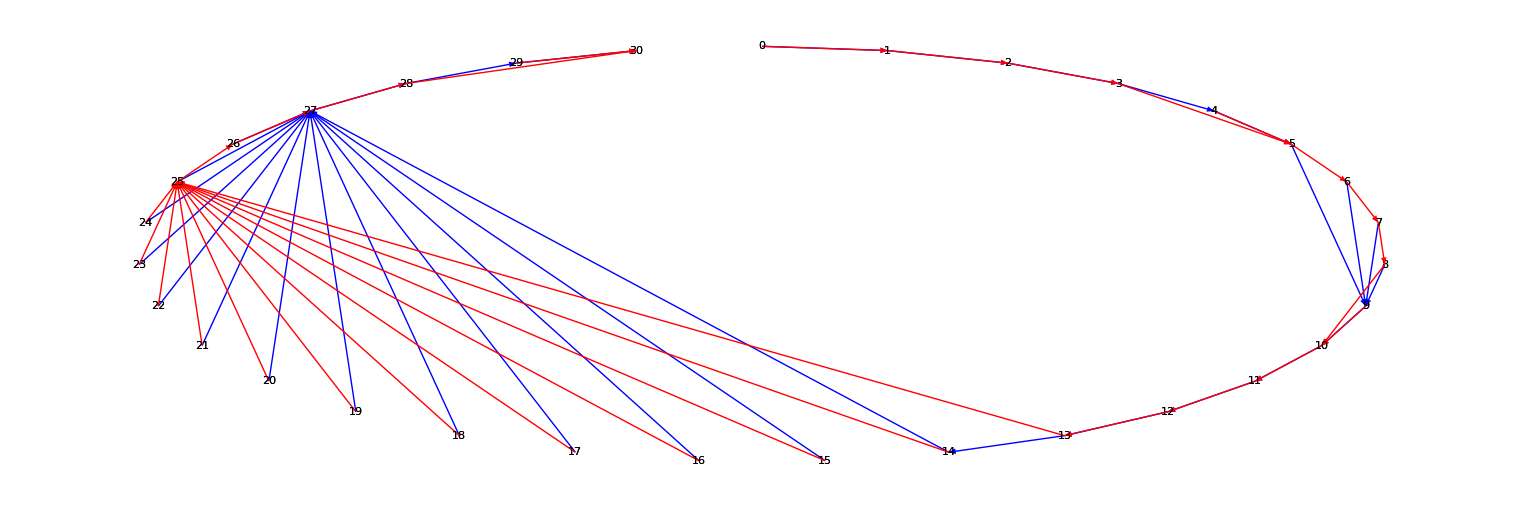

```mathematica
Show[
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{3}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{3*Sin[i*2*Pi / 31], Cos[i * 2 * Pi / 31]}, {i,0,range}],
ImageSize->Large,
EdgeRenderingFunction->({Blue, Arrowheads[.01],Arrow[#1]}&)
]
],
With[{range=30},
GraphPlot[
CombineGraphs[
Table[
GraphFromVotesShort[VoteList[start,range,{5}], start],
{start,0,range-1}]
],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{3*Sin[i*2*Pi / 31], Cos[i * 2 * Pi / 31]}, {i,0,range}],
ImageSize->Large,
EdgeRenderingFunction->({Red, Arrowheads[.01],Arrow[#1]}&)
]
]
]
```

```mathematica
With[{range=50},
GraphPlot[
{
Table[
GraphFromVotes[VoteList[start,range,{3}], start, Directive[{Red}]],
{start,0,range-1}]
,
Table[
GraphFromVotes[VoteList[start,range,{5}], start, Directive[{Blue}]],
{start,0,range-1}]
},
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->None,
DirectedEdges->False,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 50], Cos[i * 2 * Pi / 50]}, {i,0,range}],
ImageSize->Large
]
]
```

GraphPlot::grph: {{« 1 »}, {« 1 »}} is not a valid graph.

GraphPlot[«1»]

```mathematica
VoteGraph[0,50, {3,5}]
```

{0→0,0→0,1→1,1→1,2→3,2→2,3→3,3→5,5→9,5→5,9→9,9→10,10→10,10→10,11→12,11→11,12→12,12→12,13→13,13→25,25→27,25→25,27→27,27→27,28→28,28→30,30→30,30→30,31→31,31→31,32→36,32→32,36→36,36→36,37→37,37→37,38→39,38→50,50→81,50→50}

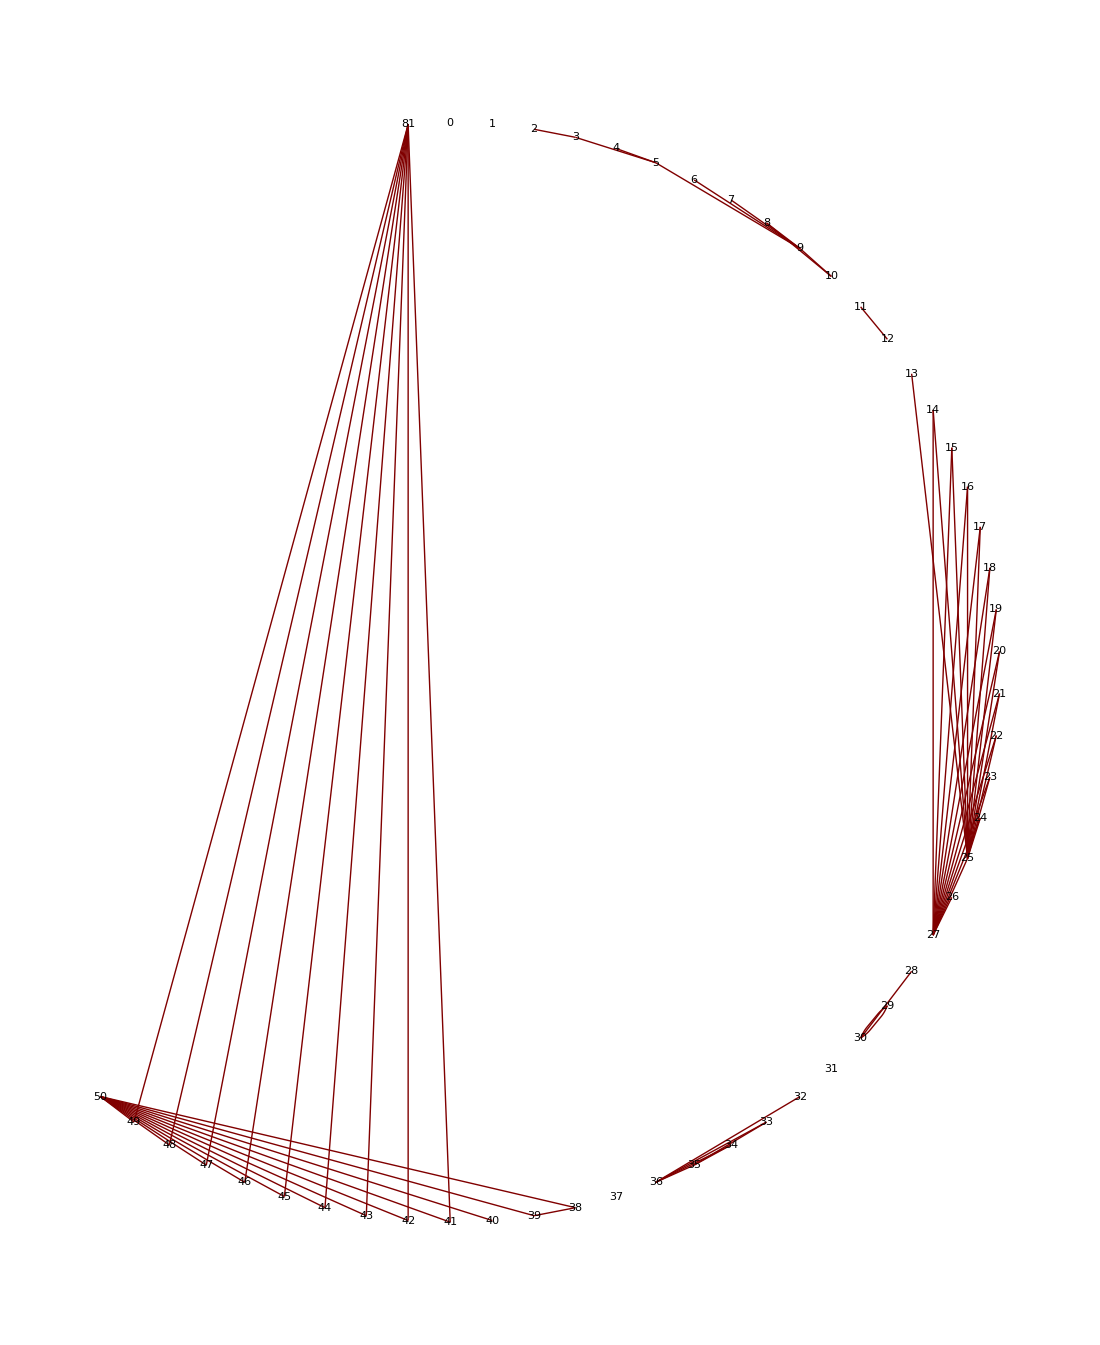

```mathematica
With[{range=50},
GraphPlot[
VoteGraph[0,49, {3,5}],
 EdgeLabeling->False,
VertexLabeling->True,
MultiedgeStyle->Automatic,
DirectedEdges->False,
SelfLoopStyle->None,
VertexCoordinateRules->Table[i->{Sin[i*2*Pi / 82], Cos[i * 2 * Pi / 82]}, {i,0,100}],
ImageSize->Large
]
]
```